#### Preamble

```mathematica
ClearAll@@{$Context<>"*"}
SetDirectory[NotebookDirectory[]]
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; 
StartScheduledTask[saveTask] (*Saves nb each 15 minutes*) ;
```

/home/juanathan/Documentos/MSc_Thesis/1-FEM-Theory

#### Plots format

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
colors[[1]] = ColorData[3,2];
PrependTo[colors,Black];
```

```mathematica
fs=9;
cdata3 = Table[ColorData[3,i],{i,10}];cdata3[[3]] = Purple;
texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
```

```mathematica
graphsOpts:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->200,PlotStyle->colors}
```

## First order 1D Element

```mathematica
pts = IdentityMatrix[4];
pts = Table[{i/3, pts[[i + 1, j]]}, {j, 4}, {i, 0, 3}];

poly = InterpolatingPolynomial[#, x] & /@ pts;
poly = FullSimplify[poly];
TeXForm /@ (FullSimplify@InterpolatingPolynomial[#, {ξ}] & /@ pts)
```

{-\frac{1}{2} (\xi -1) (3 \xi -2) (3 \xi -1),\frac{9}{2} (\xi -1) \xi  (3 \xi -2),-\frac{9}{2} (\xi -1) \xi  (3 \xi -1),\frac{9}{2} (\xi -1) \xi ^2+\xi}

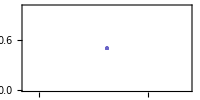

frame.pdf

```mathematica
ListPlot[{{1, 1}/2},graphsOpts,   AspectRatio -> 1/2,PlotRange -> {{-.1,1.1},{0,1}}]
Export["frame.pdf",%];
```

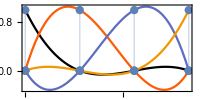

1D-ements.pdf

```mathematica
graph = Show[{Plot[poly, {x, 0, 1}, PlotRange -> All, Mesh -> None, 
   Filling -> None, Evaluate[graphsOpts],
   FillingStyle -> Directive[ColorData[6], Opacity[.2]], 
   AspectRatio -> 1/2]
  ,
  ListPlot[Flatten[pts, 1], Filling -> Axis, 
   PlotStyle -> PointSize[0.03]]}]
   
Export["1D-ements.pdf",graph]
```

## Second order 2D Element

```mathematica
pts = {{0, 0}, {1/2, 0}, {1, 0}, {0, 1/2}, {1/2, 1/2}, {0, 1}};
pts = Table[ MapThread[{#1, #2} &, {pts, IdentityMatrix[6][[i]]}], {i, 6}];
𝒟 =   MeshRegion[{{0, 0}, {1, 0}, {0, 1}}, Triangle[{1, 2, 3}]];
```

```mathematica
poly = InterpolatingPolynomial[#, {x, y}] & /@ pts;
poly = FullSimplify[poly]
TeXForm /@ (FullSimplify@InterpolatingPolynomial[#, {Subscript[ξ, 1], Subscript[ξ, 2]}] & /@ pts)
```

{(-1+x+y) (-1+2 x+2 y),-4 x (-1+x+y),x (-1+2 x),-4 y (-1+x+y),4 x y,y (-1+2 y)}

{\left(\xi _1+\xi _2-1\right) \left(2 \xi _1+2 \xi _2-1\right),-4 \xi _1 \left(\xi _1+\xi _2-1\right),\xi _1 \left(2 \xi _1-1\right),-4 \xi _2 \left(\xi _1+\xi _2-1\right),4 \xi _1 \xi _2,\xi _2 \left(2 \xi _2-1\right)}

```mathematica
ticks = Join[Table[{i,Null,.01},{i,0,1,.1}], Table[{i,Null,.025},{i,0,1,.5}]]

cp = ContourPlot[#, {x, y} ∈ 𝒟,
     PlotRange -> All,
     Contours -> 30,
     Axes -> False,
     PlotPoints -> 25,
     PlotRangePadding -> 0,
     Frame -> False,
     ColorFunctionScaling -> True,
     ColorFunction -> ColorData["SunsetColors"]] & /@ poly;
     
plot3d = Plot3D[poly[[#]], {x, y} ∈ 𝒟,
     PlotRange -> Full,
     Ticks -> {ticks,ticks,ticks},
     Mesh -> None,
     BaseStyle -> texStyle,
     Boxed -> False,
     AxesEdge -> {{-1, -1}, {-1, -1}, {-1, 1}},
     PlotStyle -> Directive[Opacity[.5]],
     ColorFunctionScaling -> True,
     ColorFunction -> ColorData["SunsetColors"],
     ImageSize -> 213*1] & /@ Range[1, Length[poly]];

level = -.0; 
gr =  Graphics3D[{Opacity[.5],Texture[#], EdgeForm[],
             Polygon[{{0, 0, level}, {0, 1, level}, {1, 0, level}}, 
             VertexTextureCoordinates -> {{0, 0}, {0, 1}, {1, 0}}]}, 
            Lighting -> "Neutral"] & /@ cp;

ref = ListPointPlot3D[Partition[Flatten[pts], 3],  PlotStyle -> PointSize[0.03], Filling -> Bottom];

graphs = MapThread[Show[{#1, #2, ref},
   PlotRange -> All,
   BoxRatios -> {1, 1, .5},
   ViewPoint -> {-1.75, -2, 1},
   ImageSize-> 180
   ] &, {plot3d, gr}]
   
Export["2D-element-"<>ToString[#]<>".svg",graphs[[#]] ] &/@Range[1,Length[graphs]]
```

{{0.,Null,0.01},{0.1,Null,0.01},{0.2,Null,0.01},{0.3,Null,0.01},{0.4,Null,0.01},{0.5,Null,0.01},{0.6,Null,0.01},{0.7,Null,0.01},{0.8,Null,0.01},{0.9,Null,0.01},{1.,Null,0.01},{0.,Null,0.025},{0.5,Null,0.025},{1.,Null,0.025}}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{2D-element-1.svg,2D-element-2.svg,2D-element-3.svg,2D-element-4.svg,2D-element-5.svg,2D-element-6.svg}

## Lowest order 2D Nédélec Element

```mathematica
pts = {{0, 0}, {1, 0}, {0, 1}};
𝒟 =  MeshRegion[{{0, 0}, {1, 0}, {0, 1}}, Triangle[{1, 2, 3}]];
```

```mathematica
edges = Permutations[pts, {2}];
edges = edges[[#]] & /@ {1, -3, -2};
len = Norm /@ Differences /@ edges
```

{1,√2,1}

```mathematica
poly = Table[ MapThread[{#1, #2} &, {pts, IdentityMatrix[3][[i]]}], {i, 3}];
poly = InterpolatingPolynomial[#, {x, y}] & /@ poly;
poly = Permutations[poly, {2}];
poly = poly[[#]] & /@ {1, -3, -2}
```

{{1-x-y,x},{x,y},{y,1-x-y}}

```mathematica
nedelec = #1*Grad[#2, {x, y}] - #2*Grad[#1, {x, y}] &
vec = len*(nedelec @@ # & /@ poly)
```

#1 #2{x,y}-#2 #1{x,y}&

{{1-y,x},{-√2 y,√2 x},{-y,-1+x}}

{{0.,Null,0.005},{0.1,Null,0.005},{0.2,Null,0.005},{0.3,Null,0.005},{0.4,Null,0.005},{0.5,Null,0.005},{0.6,Null,0.005},{0.7,Null,0.005},{0.8,Null,0.005},{0.9,Null,0.005},{1.,Null,0.005},{0.,Null,0.02},{0.5,Null,0.02},{1.,Null,0.02}}

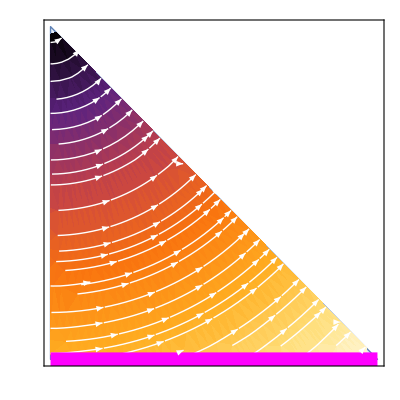
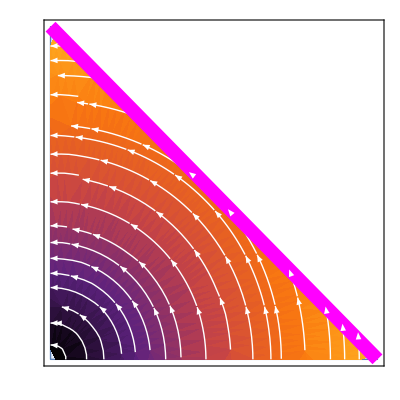
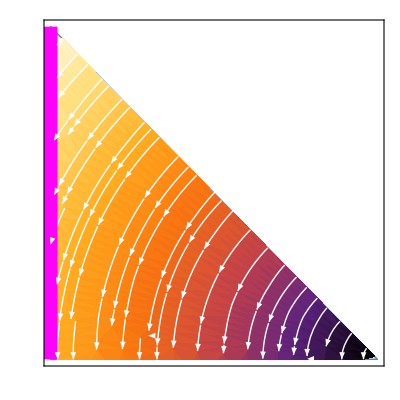

{2D-Nedelec1.svg,2D-Nedelec2.svg,2D-Nedelec3.svg}

```mathematica
ticks = Join[Table[{i,Null,.005},{i,0,1,.1}], Table[{i,Null,.02},{i,0,1,.5}]]


plot = StreamDensityPlot[#, {x, y} ∈ 𝒟, 
    ColorFunction -> ColorData["SunsetColors"],
    StreamScale -> Large,
    StreamPoints -> Medium,
    StreamStyle -> White,
    StreamColorFunction -> None,
    Frame -> {{True, False}, {True, False}},
    FrameTicks -> None
    ] & /@ vec;

plot = MapThread[
 Show[{#1, 
    Graphics[{Thickness[.025], Magenta, Line[#2]}]}] &, {plot, 
  edges}]
  
Export["2D-Nedelec"<>ToString[#]<>".svg", plot[[#]]]&/@{1,2,3}
```

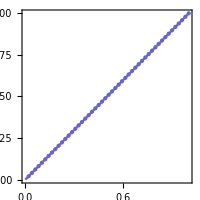

2D-NedelecFrame.pdf

{{1-ξ_2,ξ_1},{-√2 ξ_2,√2 ξ_1},{-ξ_2,-1+ξ_1}}

{\left\{1-\xi _2,\xi _1\right\},\left\{-\sqrt{2} \xi _2,\sqrt{2} \xi _1\right\},\left\{-\xi _2,\xi _1-1\right\}}

```mathematica
frame = Plot[x, {x, 0, 1}, Frame -> {{True, False}, {True, False}},Evaluate@graphsOpts, AspectRatio -> 1]
Export["2D-NedelecFrame.pdf", frame]

algo = vec /.{x-> Subscript[ξ, 1],y->  Subscript[ξ, 2], z->  Subscript[ξ, 3]}
TeXForm/@ algo
```

## Lowest order 3D Nédélec Element

```mathematica
pts = {{0, 0, 0}, {1, 0, 0},{0, 1, 0}, {0, 0, 1}};
𝒟 = MeshRegion[pts, Tetrahedron[{1, 2, 3, 4}]];
```

```mathematica
edges = Partition[#, 3] &@Permutations[pts, {2}];
edges = Flatten[edges, 1][[#]] & /@ {1, 5, 7,3,11,9}
len = Norm /@ Differences /@ edges
```

{{{0,0,0},{1,0,0}},{{1,0,0},{0,1,0}},{{0,1,0},{0,0,0}},{{0,0,0},{0,0,1}},{{0,0,1},{1,0,0}},{{0,1,0},{0,0,1}}}

{1,√2,1,1,√2,√2}

```mathematica
poly = Table[    MapThread[{#1, #2} &, {pts, IdentityMatrix[4][[i]]}], {i, 4}];
poly = InterpolatingPolynomial[#, {x, y, z}] & /@ poly
poly = Partition[#, 3] &@Permutations[poly, {2}];
poly = Flatten[poly, 1][[#]] & /@ {1, 5, 7,3,11,9}
```

{1-x-y-z,x,y,z}

{{1-x-y-z,x},{x,y},{y,1-x-y-z},{1-x-y-z,z},{z,x},{y,z}}

```mathematica
ticks = Join[Table[{i,Null,.01},{i,0,1,.1}], Table[{i,Null,.025},{i,0,1,.5}]]
nedelec = #1*Grad[#2, {x, y, z}] - #2*Grad[#1, {x, y, z}] &
vec = len *( nedelec @@ # & /@ poly)
plot = VectorPlot3D[#, {x, y, z} ∈ 𝒟, 
    ImageSize -> 215,
    Boxed -> False,
    PlotRange -> All,
       Ticks -> {ticks,ticks,ticks},
    BoxRatios -> {1, 1, 1},
   ViewPoint -> {-1., -2, 1},
    AxesEdge -> {{-1, -1}, {-1, -1}, {-1, -1}},
    VectorSizes -> Medium,
    VectorScaling -> Automatic,
    VectorAspectRatio -> 1/2,
    VectorMarkers -> {"Arrow3D", "Start"},
    VectorPoints -> 8,
    VectorColorFunction -> ColorData["SunsetColors"]
    ] & /@ vec;
    
plot = MapThread[
 Show[{#1, 
    Graphics3D[{Thickness[.025], Magenta, 
      Line[#2]}] }] &, {plot, edges}]

Export["3D-Nedelec"<>ToString[#]<>".svg", plot[[#]]]&/@{1,2,3,4,5,6}
```

{{0.,Null,0.01},{0.1,Null,0.01},{0.2,Null,0.01},{0.3,Null,0.01},{0.4,Null,0.01},{0.5,Null,0.01},{0.6,Null,0.01},{0.7,Null,0.01},{0.8,Null,0.01},{0.9,Null,0.01},{1.,Null,0.01},{0.,Null,0.025},{0.5,Null,0.025},{1.,Null,0.025}}

#1 #2{x,y,z}-#2 #1{x,y,z}&

{{1-y-z,x,x},{-√2 y,√2 x,0},{-y,-1+x+z,-y},{z,z,1-x-y},{√2 z,0,-√2 x},{0,-√2 z,√2 y}}

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

{3D-Nedelec1.svg,3D-Nedelec2.svg,3D-Nedelec3.svg,3D-Nedelec4.svg,3D-Nedelec5.svg,3D-Nedelec6.svg}

```mathematica
algo = vec /.{x-> Subscript[ξ, 1],y->  Subscript[ξ, 2], z->  Subscript[ξ, 3]}
TeXForm/@ algo
```

{{1-ξ_2-ξ_3,ξ_1,ξ_1},{-√2 ξ_2,√2 ξ_1,0},{-ξ_2,-1+ξ_1+ξ_3,-ξ_2},{ξ_3,ξ_3,1-ξ_1-ξ_2},{√2 ξ_3,0,-√2 ξ_1},{0,-√2 ξ_3,√2 ξ_2}}

{\left\{-\xi _2-\xi _3+1,\xi _1,\xi _1\right\},\left\{-\sqrt{2} \xi _2,\sqrt{2} \xi _1,0\right\},\left\{-\xi _2,\xi _1+\xi _3-1,-\xi _2\right\},\left\{\xi _3,\xi _3,-\xi _1-\xi _2+1\right\},\left\{\sqrt{2} \xi _3,0,-\sqrt{2} \xi _1\right\},\left\{0,-\sqrt{2} \xi _3,\sqrt{2} \xi _2\right\}}

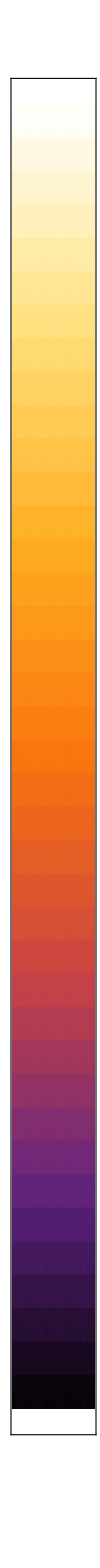

-Graphics-

leg.svg

leg-frame.pdf

```mathematica
leg =  DensityPlot[y, {x, 0,1}, {y, 0, 1}, BaseStyle -> texStyle, 
  FrameTicks -> {{None, None}, {None, None}},
  FrameStyle -> Black, 
  AspectRatio -> 30, 
  PlotRange -> All, ColorFunction -> "SunsetColors", 
  PlotPoints -> 40, PlotRangePadding -> None, 
 ImageSize -> Reverse@{60, 25/2}*8]
 
 frameColor = ListPlot[{{.5,.5}}, BaseStyle -> texStyle, Frame->True,
  FrameTicks -> {{None, None}, {None, None}},
  FrameStyle -> Black, 
  AspectRatio -> 30, 
  PlotRange -> All, ColorFunction -> "SunsetColors", 
 ImageSize -> Reverse@{60, 25/2}*8]
 
 Export["leg.svg",leg]
 Export["leg-frame.pdf",frameColor]
```